## Private 私有函数

### TEST 性能测试

返回循环 n 遍所花费的时间和结果

```mathematica
ClearAll[TEST];

Attributes[TEST]={HoldAll};

TEST[code_,n_:1]:=Module[{},
ClearSystemCache[];
(Do[code,n-1];code)//AbsoluteTiming
]

TEST[Limit[(x^2+1)/(2 x^2-1),x->∞],1000]
```

{0.634296,1/2}

### ExpressionPivot 表达式主元

返回首个匹配到的非数值符号

```mathematica
ClearAll[ExpressionPivot];

Attributes[ExpressionPivot]={Listable};

ExpressionPivot[expr_]:=FirstCase[expr,_Symbol?(Not@*NumericQ),Symbol,{-1}];

TEST[{ExpressionPivot[{1,x,a/(a+b),E^x}]},10000]
```

{0.0641907,{{Symbol,x,a,x}}}

### CoefficientSeparation 系数分割

返回匹配到的系数和余下部分

```mathematica
ClearAll[CoefficientSeparation];

Attributes[CoefficientSeparation]={Listable};

CoefficientSeparation[expr_,x_]/;FreeQ[expr,x]:={expr,1};
CoefficientSeparation[expr_,x_]:=Replace[expr,Longest[c_.]r_/;FreeQ[c,x]->{c,r}];

TEST[CoefficientSeparation[{0,(a+b)/2,2/(a+b),(a+b)/(2x),x,-x,2a Sin[x]+4a x,2a Sin[x]+4a x//Simplify},x],10000]
```

{0.634796,{{0,1},{(a+b)/2,1},{2/(a+b),1},{(a+b)/2,1/x},{1,x},{-1,x},{1,4 a x+2 a Sin[x]},{2 a,2 x+Sin[x]}}}

### FirstCoefficient 首系数

返回最高次项的系数

```mathematica
ClearAll[FirstCoefficient];

Attributes[FirstCoefficient]={Listable};

FirstCoefficient[poly_,x_]:=Coefficient[poly,x,Exponent[poly,x]];

TEST[FirstCoefficient[{1,3 x^3-x^2+1,-1/4 x^2+1},x],10000]
```

{0.106653,{1,3,-1/4}}

### PolynomialRoots 多项式根集

返回多项式的根集，速度是 SolveValues 的 7 倍
ToRadicals：是否尝试将结果转换成根式

```mathematica
ClearAll[PolynomialRoots];

Attributes[PolynomialRoots]={Listable};
Options[PolynomialRoots]={ToRadicals->False};

PolynomialRoots[a_,x_,OptionsPattern[]]/;FreeQ[a,x]:={};
PolynomialRoots[a_.x_+b_.,x_,OptionsPattern[]]/;FreeQ[{a,b},x]:={-b/a};
PolynomialRoots[poly_,x_,OptionsPattern[]]:=List@@(Roots[poly==0,x,Cubics->OptionValue@ToRadicals,Quartics->OptionValue@ToRadicals]/.Equal->(#2&));

TEST[SolveValues[#==0,x,Cubics->False,Quartics->False]&/@{1,2x-1,3 x^2-4,x^3-x+1,2 x^4-x+1}//Column,100]
TEST[PolynomialRoots[{1,2x-1,3 x^2-4,x^3-x+1,2 x^4-x+1},x]//Column,100]
```

{0.196111,{}
{1/2}
{-2/(√3),2/(√3)}
{Root-1.32Root[1-#1+#1^3&,1]-1.324717957244746,Root0.662-0.562 ⅈRoot[1-#1+#1^3&,2]0.662358978622373,Root0.662+0.562 ⅈRoot[1-#1+#1^3&,3]0.662358978622373}
{Root-0.607-0.758 ⅈRoot[1-#1+2 #1^4&,1]-0.606835562799765,Root-0.607+0.758 ⅈRoot[1-#1+2 #1^4&,2]-0.606835562799765,Root0.607-0.403 ⅈRoot[1-#1+2 #1^4&,3]0.606835562799765,Root0.607+0.403 ⅈRoot[1-#1+2 #1^4&,4]0.606835562799765}}

{0.0291863,{}
{1/2}
{2/(√3),-2/(√3)}
{Root-1.32Root[1-#1+#1^3&,1]-1.324717957244746,Root0.662-0.562 ⅈRoot[1-#1+#1^3&,2]0.662358978622373,Root0.662+0.562 ⅈRoot[1-#1+#1^3&,3]0.662358978622373}
{Root-0.607-0.758 ⅈRoot[1-#1+2 #1^4&,1]-0.606835562799765,Root-0.607+0.758 ⅈRoot[1-#1+2 #1^4&,2]-0.606835562799765,Root0.607-0.403 ⅈRoot[1-#1+2 #1^4&,3]0.606835562799765,Root0.607+0.403 ⅈRoot[1-#1+2 #1^4&,4]0.606835562799765}}

### ArcTanLimitAtPositiveInfinity 反正切正无穷处极限

返回 lim_(x->∞) arctan f(x) ，速度是 Limit 的 7 倍

```mathematica
ClearAll[ArcTanLimitAtPositiveInfinity];

Attributes[ArcTanLimitAtPositiveInfinity]={Listable};

ArcTanLimitAtPositiveInfinity[expr_,x_]:=Module[{nd,e,r},
nd=NumeratorDenominator@Together@expr;
e=Exponent[nd,x];
r=Divide@@Coefficient[nd,x,e];
Piecewise[{{Sign@r π/2, Subtract@@e>0}, {0, Subtract@@e<0}, {ArcTan@r, True}}]
];

TEST[Limit[{ArcTan@(2/(-3 x^2-1)),ArcTan@((2x+1)/(-3 x^3-1)),ArcTan@((2 x^2+1)/(-3 x^2-1)),ArcTan@((-5 x^2+1)/(-4 x^2-1))},x->∞],100]
TEST[ArcTanLimitAtPositiveInfinity[{2/(-3 x^2-1),(2x+1)/(-3 x^3-1),(2 x^2+1)/(-3 x^2-1),(-5 x^2+1)/(-4 x^2-1)},x],100]
```

{0.340464,{0,0,-ArcTan[2/3],ArcTan[5/4]}}

{0.0443135,{0,0,-ArcTan[2/3],ArcTan[5/4]}}

## Pubic 公有函数

### IBP 分部积分法

返回分部后的结果
Assumptions：假设，辅助化简

```mathematica
ClearAll[IBP];

Options[IBP]={Assumptions->$Assumptions};

IBP[u_,v_,x_Symbol,OptionsPattern]:=Module[{coef,rem},
{coef,rem}=CoefficientSeparation[v D[u,x],x];
u v-coef remx
];
IBP[f_,x_Symbol,OptionsPattern[]]:=IBP[f,x,x];

IBP[u_,v_,{x_Symbol,a_,b_},OptionsPattern[]]:=Module[{assum=OptionValue@Assumptions,c,r},
{c,r}=CoefficientSeparation[v D[u,x],x];
Limit[u v,x->b,Assumptions->assum]-Limit[u v,x->a,Assumptions->assum]-c rxab
];
IBP[f_,{x_Symbol,a_,b_},opts:OptionsPattern[]]:=IBP[f,x,{x,a,b},opts];

TEST[IBP[a x^2+b x+c,Sin[α x],x]]
TEST[IBP[Sin[α Log[x]],{x,0,1},Assumptions->α>0]]
```

{0.0000219,IBP[c+b x+a x^2,Sin[x α],x]}

{0.545347,-α Cos[α Log[x]]x01}

### IBS 换元积分法

返回换元后的结果
Assumptions：辅助化简
Inactive：是否返回不激活的积分形式

```mathematica
ClearAll[IBS];

Options[IBS]={Assumptions->$Assumptions,Inactive->False};

IBS[f_,ex_->et_,x_Symbol,t_Symbol,OptionsPattern[]]/;FreeQ[ex,t]&&!FreeQ[ex,x]&&FreeQ[et,x]&&!FreeQ[et,t]:=
Module[{assum=OptionValue@Assumptions,inactive=OptionValue@Inactive,u,result,c,r},
result=If[ex===x,f/.x->et,IntegrateChangeVariables[fx,u,u==ex,Assumptions->assum]⟦1⟧/.C@_->0/.u->et]D[et,t];
If[inactive,{c,r}=CoefficientSeparation[Together@result,t];c rt,result]
];
IBS[f_,x_Symbol->et_,t_Symbol,opts:OptionsPattern[]]:=IBS[f,x->et,x,t,opts];
IBS[f_,ex_->t_Symbol,x_Symbol,opts:OptionsPattern[]]:=IBS[f,ex->t,x,t,opts];
IBS[f_,ex_->et_,opts:OptionsPattern[]]:=IBS[f,ex->et,ExpressionPivot@ex,ExpressionPivot@et,opts];

IBS[f_,{a_,b_},ex_->et_,x_Symbol,t_Symbol,OptionsPattern[]]/;FreeQ[ex,t]&&!FreeQ[ex,x]&&FreeQ[et,x]&&!FreeQ[et,t]:=
Module[{assum=OptionValue@Assumptions,u,temp,result,aa,bb,c,r},
temp=If[ex===x,fxab/.x->u,IntegrateChangeVariables[fxab,u,u==ex,Assumptions->assum]];
{result,{t,aa,bb}}=List@@If[et===t,temp/.u->t,IntegrateChangeVariables[temp,t,u==et,Assumptions->assum]];
{c,r}=CoefficientSeparation[Together@result,t];
c rtab
];
IBS[f_,{a_,b_},x_Symbol->et_,t_Symbol,opts:OptionsPattern[]]:=IBS[f,{a,b},x->et,x,t,opts];
IBS[f_,{a_,b_},ex_->t_Symbol,x_Symbol,opts:OptionsPattern[]]:=IBS[f,{a,b},ex->t,x,t,opts];
IBS[f_,{a_,b_},ex_->et_,opts:OptionsPattern[]]:=IBS[f,{a,b},ex->et,ExpressionPivot@ex,ExpressionPivot@et,opts];

TEST[{
IBS[1,x->t^2],
IBS[x^2,x->Sin[θ]],
IBS[1/(1+E^x),E^x->Tan[t]/2,Inactive->True]
}//Column]
TEST[IBS[x^2,{0,1},2x->E^t]]
```

{0.0175988,2 t
Cos[θ] Sin[θ]^2
2 (Csc[t] Sec[t])/(2+Tan[t])t}

{0.134138,1/8 ⅇ^(3 t)t01}

### ApartArcTan 反正切裂项

返回反正切裂项的结果
原理：使用公式 arctan f(x)=∑_(k:f(x)=i) (x-Re k)/(Im k)+C 进行裂项，其中分段常数 C 可由如下方法计算而出：先计算 lim_(x->∞) arctan f(x) 获得基准常数 C_0 ，然后通过数值近似得出各段常数，不难证明它们必为 C_0+n π 形式，速度是计算极点左右极限差的 32 倍
GenerateConstant：是否生成分段常数
SimplifyFunction：化简函数

```mathematica
ClearAll[ApartArcTan];

Attributes[ApartArcTan]={Listable};
Options[ApartArcTan]={GenerateConstant->True,SimplifyFunction->ToRadicals/*ComplexExpand/*FunctionExpand/*Simplify};

ApartArcTan[expr_,x_Symbol,OptionsPattern[]]/;RationalExpressionQ[expr,x]:=
Module[{result,count=0,poles,sample,c={}},
result=Sum[ArcTan@OptionValue[SimplifyFunction]@((x-Re@r)/((count+=Sign@#;#)&@Im@r)),{r,SolveValues[expr-I==0,x]}];
If[OptionValue@GenerateConstant,
result+=ArcTanLimitAtPositiveInfinity[expr,x]-count π/2;
poles=DeleteDuplicates@SolveValues[Denominator@Together@expr==0,x,Reals];
If[Length@poles=!=0,
sample=1/2 Table[#[[i]]+#[[i+1]],{i,Length@#-1}]&@Prepend[#,First@#-1]&@N@poles;
c=π Round[1/π Table[ArcTan@expr-result/.x->i,{i,sample}]];
result+=Piecewise@Prepend[Table[{c⟦i+1⟧,poles⟦i⟧<x<poles⟦i+1⟧},{i,Length@poles-1}],{First@c,x<First@poles}]
];
];
result
];
ApartArcTan[expr_,opts:OptionsPattern[]]:=ApartArcTan[expr,ExpressionPivot@expr,opts];

TEST[ApartArcTan[{1,x,1/x,(2x)/(1-x^2),x^2+1,(x+√2)/(1-√2 x),t+1/t,x^2/(x^4-1)}]//Column]
```

{0.0963898,π/4
ArcTan[x]
π/2-ArcTan[x]+(Piecewise[{{-π, x<0}, {0, True}}])
-π+2 ArcTan[x]+(Piecewise[{{2 π, x<-1}, {π, -1<x<1}, {0, True}}])
π/2+ArcTan[(-√(2-√2)-2^(3/4) x)/(√(2+√2))]+ArcTan[(-√(2-√2)+2^(3/4) x)/(√(2+√2))]
-π/2-ArcTan[1/(√2)]+ArcTan[x]+(Piecewise[{{π, x<1/(√2)}, {0, True}}])
π/2-ArcTan[(2 t)/(-1+√5)]+ArcTan[(2 t)/(1+√5)]+(Piecewise[{{-π, t<0}, {0, True}}])
ArcTan[(-1+√3-2 √2 x)/(1+√3)]+ArcTan[(1+√3-2 √2 x)/(-1+√3)]+ArcTan[(-1+√3+2 √2 x)/(1+√3)]+ArcTan[(1+√3+2 √2 x)/(-1+√3)]+(Piecewise[{{0, x<-1}, {-π, -1<x<1}, {0, True}}])}

### ComplexFactor 复因式分解

返回复数域中因式分解的结果
ToRadicals：是否尝试将结果转换为根式

```mathematica
ClearAll[ComplexFactor];

Attributes[ComplexFactor]={Listable};
Options[ComplexFactor]=Options[PolynomialRoots];

ComplexFactor[poly_,x_Symbol,OptionsPattern[]]/;PolynomialQ[poly,x]:=FirstCoefficient[poly,x]Times@@(x-PolynomialRoots[poly,x,ToRadicals->OptionValue@ToRadicals]);
ComplexFactor[poly_,opts:OptionsPattern[]]:=ComplexFactor[poly,ExpressionPivot@poly,opts];

TEST[ComplexFactor[{1,2x-1,3 x^2-4,x^3-x+1,2 x^4-x+1}],1000]
```

{0.549266,{1,2 (-1/2+x),3 (-2/(√3)+x) (2/(√3)+x),(x-Root-1.32Root[1-#1+#1^3&,1]-1.324717957244746) (x-Root0.662-0.562 ⅈRoot[1-#1+#1^3&,2]0.662358978622373) (x-Root0.662+0.562 ⅈRoot[1-#1+#1^3&,3]0.662358978622373),2 (x-Root-0.607-0.758 ⅈRoot[1-#1+2 #1^4&,1]-0.606835562799765) (x-Root-0.607+0.758 ⅈRoot[1-#1+2 #1^4&,2]-0.606835562799765) (x-Root0.607-0.403 ⅈRoot[1-#1+2 #1^4&,3]0.606835562799765) (x-Root0.607+0.403 ⅈRoot[1-#1+2 #1^4&,4]0.606835562799765)}}

### ComplexApart 复裂项

返回复数域中裂项的结果
ToRadicals：是否尝试将结果转换为根式

```mathematica
ClearAll[ComplexApart];

Attributes[ComplexApart]={Listable};
Options[ComplexApart]=Options[ComplexFactor];

ComplexApart[expr_,x_Symbol,OptionsPattern[]]/;RationalExpressionQ[expr,x]:=Apart[#1/ComplexFactor[#2,x,ToRadicals->OptionValue@ToRadicals],x]&@@NumeratorDenominator@Together@expr;
ComplexApart[poly_,opts:OptionsPattern[]]:=ComplexApart[poly,ExpressionPivot@poly,opts];

TEST[ComplexApart[{1,(x+2)/(2x-1),(4 x^4+2 x^2-x+1)/(3 x^2-4),(x+1)^2/(2 (x^2+1)^2 (x-2)^2)}]//Column,100]
```

{0.300815,1
1/2+5/(2 (-1+2 x))
22/9+(-97+6 √3)/(12 √3 (2 √3-3 x))+(4 x^2)/3+(-97-6 √3)/(12 √3 (2 √3+3 x))
9/(50 (-2+x)^2)-21/(125 (-2+x))+(1/25-(3 ⅈ)/100)/(-ⅈ+x)^2+(21/250-(19 ⅈ)/500)/(-ⅈ+x)+(1/25+(3 ⅈ)/100)/(ⅈ+x)^2+(21/250+(19 ⅈ)/500)/(ⅈ+x)}

### RealFactor 实因式分解

返回实数域中因式分解的结果
SimplifyFunction：化简函数

```mathematica
ClearAll[RealFactor];

Attributes[RealFactor]={Listable};
Options[RealFactor]={SimplifyFunction->ToRadicals/*ComplexExpand/*FunctionExpand/*Simplify};

RealFactor[poly_,x_Symbol,OptionsPattern[]]/;PolynomialQ[poly,x]:=
FirstCoefficient[poly,x]Times@@Table[OptionValue[SimplifyFunction]@Piecewise[{{x-r, r∈Reals}, {(x-Re@r)^2+(Im@r)^2, True}}],{r,DeleteDuplicates[PolynomialRoots[poly,x],N[#1*==#2]&]}]
RealFactor[poly_,opts:OptionsPattern[]]:=RealFactor[poly,ExpressionPivot@poly,opts];

TEST[RealFactor[{1,x-1,x^2+1,x^2-1,x^4-x^2+x-1,x^4+1,x^5-1}]//Column,1]
```

{0.310676,1
-1+x
1+x^2
(-1+x) (1+x)
1/6 (-1+x) (2+2^(2/3) (29-3 √93)^(1/3)+2^(2/3) (29+3 √93)^(1/3)+6 x) ((-(58-6 √93)^(1/3)+(29-3 √93)^(2/3)+(29+3 √93)^(2/3)-(58+6 √93)^(1/3))/(9 2^(2/3))-1/6 (-4+2^(2/3) (29-3 √93)^(1/3)+2^(2/3) (29+3 √93)^(1/3)) x+x^2)
(1-√2 x+x^2) (1+√2 x+x^2)
1/4 (-1+x) (2+x-√5 x+2 x^2) (2+x+√5 x+2 x^2)}

### RealApart 实裂项

返回实数域中因式分解的结果
SimplifyFunction：化简函数

```mathematica
ClearAll[RealApart];

Attributes[RealApart]={Listable};
Options[RealApart]=Options[RealFactor];

RealApart[expr_,x_Symbol,opts:OptionsPattern[]]/;RationalExpressionQ[expr,x]:=Apart[#1/RealFactor[#2,x,SimplifyFunction->OptionValue@SimplifyFunction],x]&@@NumeratorDenominator@Together@expr;
RealApart[expr_,opts:OptionsPattern[]]:=RealApart[expr,ExpressionPivot@expr,opts];

TEST[RealApart[{1,1/(x^4+1),1/(x^2-5),1/(x^4+x^2-1)}]//Column,1]
```

{0.0572118,1
(-√2+x)/(2 √2 (-1+√2 x-x^2))+(√2+x)/(2 √2 (1+√2 x+x^2))
-1/(2 √5 (√5-x))-1/(2 √5 (√5+x))
-(√(2/(5 (-1+√5))))/(√(2 (-1+√5))-2 x)-(√(2/(5 (-1+√5))))/(√(2 (-1+√5))+2 x)-2/(√5 (1+√5+2 x^2))}

### FindIdentities 查找恒等式

TODO

```mathematica
ClearAll[FindIdentities];

FindIdentities[expr1_,expr2_,x_Symbol]/;RationalExpressionQ[expr1,x]&&RationalExpressionQ[expr2,x]:=
Module[{p1,p2,roots,limit},
p1=Numerator@Simplify@expr1 Denominator@Simplify@expr2;
p2=Numerator@Simplify@expr2 Denominator@Simplify@expr1;
roots=DeleteDuplicates@SolveValues[D[p1,x]p2==D[p2,x]p1,x];
DeleteDuplicates@Flatten@Reap[
Do[
limit=lim_(x->i) p1/p2//Simplify;
If[limit=!=0&&limit∈Rationals,
Sow[Defer@Evaluate@p1-limit p2==(p1-limit p2//Factor)]
];
,{i,roots}
]
][[2]]
];

TEST[{
FindIdentities[x^2-1,x+1,x],
FindIdentities[x^2+2x+5,(2x+3)^2,x],
FindIdentities[x^3-3 x^2-21x-25,(x+3)^3,x],
FindIdentities[4 x^3-9x+3,((x^2-3)/(x+1))^3,x]
}//Column,1]
```

{0.032523,{2 (1+x)+(-1+x^2)==(1+x)^2}
{-4/17 (3+2 x)^2+(5+2 x+x^2)==1/17 (-7+x)^2}
{(3+x)^3+(-25-21 x-3 x^2+x^3)==2 (1+x)^3}
{1/9 (-3+x^2)^3+(1+x)^3 (3-9 x+4 x^3)==1/9 x^2 (-135-180 x+18 x^2+108 x^3+37 x^4),-8/3 (-3+x^2)^3+(1+x)^3 (3-9 x+4 x^3)==1/3 (-15+9 x^2+2 x^3)^2}}

## Experimental 实验性函数

### CorrectionTest 修正测试

Skip：跳过测试项
TimeConstraint：限制各测试项计算时间
VerifyDiscontinuities：验证间断点
WorkingPrecision：工作精度

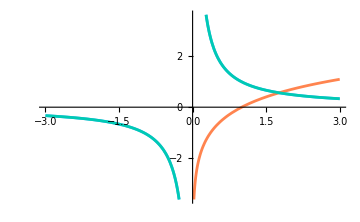
{0.0300125,定义域 | 间断点
x<0||x>0 | False
x>0 | x<0
图像 | 
-Graphics- | }

```mathematica
ClearAll[CorrectionTest];

CorrectionTest::overtime="`` 计算超时";

Options[CorrectionTest]={Skip->{},TimeConstraint->∞,VerifyDiscontinuities->{},WorkingPrecision->$MinPrecision};

CorrectionTest[org_,res_,{x_,xmin_,xmax_},OptionsPattern[]]:=
Module[{
table={{Style["定义域",Bold], Style["间断点",Bold]}, {Style[True,Bold,RGBColor["#4081ff"]], Style[False,Bold,RGBColor["#4081ff"]]}, {Style[True,Bold,RGBColor["#eb7100"]], Style[False,Bold,RGBColor["#eb7100"]]}, {Style["图像",Bold], }, {Null, }},
skip=OptionValue[Skip],
cons=OptionValue[TimeConstraint],
veri=OptionValue[VerifyDiscontinuities],
prec=OptionValue[WorkingPrecision],
dom=True
},
If[!ListQ[skip],skip={skip}];
If[!ListQ[veri],veri={veri}];
If[!AssociationQ[cons],cons=Association["定义域"->cons,"间断点"->cons,"图像"->cons]];
If[!MemberQ[skip,"定义域"],
TimeConstrained[
table⟦2,1⟧=Item[Style[dom=Reduce[FunctionDomain[org,x],x∈Reals],Bold,RGBColor["#4081ff"]],ItemSize->Automatic];
table⟦3,1⟧=Item[Style[Reduce[FunctionDomain[res,x]&&dom,x∈Reals],Bold,RGBColor["#eb7100"]],ItemSize->Automatic];
,cons["定义域"],Message[CorrectionTest::overtime,"定义域"];
];
];
If[!MemberQ[skip,"间断点"],
TimeConstrained[
table⟦2,2⟧=Item[Style[Reduce[FunctionDiscontinuities[org,x]&&dom,x∈Reals],Bold,RGBColor["#4081ff"]],ItemSize->Automatic];
table⟦3,2⟧=Item[Style[Reduce[FunctionDiscontinuities[res,x]&&dom,x∈Reals],Bold,RGBColor["#eb7100"]],ItemSize->Automatic];
,cons["间断点"],Message[CorrectionTest::overtime,"间断点"];
];
];
If[!MemberQ[skip,"图像"],
TimeConstrained[
table⟦5,1⟧=Plot[
{org,res,Evaluate[D[(res/.{Abs[p_]->Piecewise[{{p, p>0}, {-p, p<0}}],Sign[p_]->Piecewise[{{1, p>0}, {-1, p<0}}]}), x]]},{x,xmin,xmax},
PlotStyle->96,ImageSize->Medium,
Epilog->{Black,PointSize[Medium],Point[
Block[{$MinPrecision=prec},N@Table[{i,res/.x->i},{i,veri}]]
]}
],cons["图像"],Message[CorrectionTest::overtime,"图像"];
];
];
Grid[table,Alignment->{Center,Center},Spacings->{1,1},ItemSize->{Scaled[0.5],Automatic},Frame->All]
];

TEST[CorrectionTest[1/x,Log[x],{x,-3,3}],1]
```

### BivarablePlot 绘制双元关系图

PlotLabels：双元标签

```mathematica
ClearAll[BivariablePlot];

Options[BivariablePlot]={PlotLabels->None};

BivariablePlot[list_List,x_Symbol,OptionsPattern[]]:=
Module[{labels,isValid,const,constQ,edges,vertexes,usedVertexes,edgeStylize,vertexStylize},
labels=OptionValue@PlotLabels;
isValid=labels=!=None&&Length@list===Length@labels;
constQ[value_]:=FreeQ[value,x]&&!PossibleZeroQ@value;
edgeStylize[edge_,value_]:=Labeled[edge,Placed[Style[value,14,FontFamily->"CMU Serif"],.5]];
vertexStylize[value_]:=Framed[Style[value,Black,14,FontFamily->"CMU Serif"],FrameStyle->None];
edges=Table[
Piecewise[{{{bivars[[1]]<->bivars[[2]],const}, constQ[const=list[[bivars[[1]]]]^2+list[[bivars[[2]]]]^2//Simplify]}, {Piecewise[{{{bivars[[2]]->bivars[[1]],-const}, const<0//TrueQ}, {{bivars[[1]]->bivars[[2]],const}, True}}], constQ[const=list[[bivars[[1]]]]^2-list[[bivars[[2]]]]^2//Simplify]}, {Nothing, True}}]
,{bivars,Subsets[Range@Length@list,{2}]}];
usedVertexes=DeleteDuplicates@Cases[edges[[All,1]],_Integer,{2}];
vertexes=Table[i->(Evaluate@Inset[vertexStylize@Piecewise[{{labels[[i]]==list[[i]], isValid}, {list[[i]], True}}],#]&),{i,usedVertexes}];
edges=edgeStylize@@@edges;
Graph[edges,PlotTheme->"DiagramBlack",VertexLabels->None,VertexShapeFunction->vertexes,PlotRangePadding->Scaled@.1]
];

TEST[{BivariablePlot[{x+√(1-x^2),x-√(1-x^2),√(2x √(1-x^2))},x],BivariablePlot[{Cos[x]+Sin[x],Cos[x]-Sin[x],2Cos[x]+Sin[x],Cos[x]-2Sin[x]},x,PlotLabels->{p,q,m}]},1]
```

{0.153262,{-Graphics-,-Graphics-}}